```mathematica
ClearAll/@Names["Global`*"]
```

{Null,Null,Null,Null,Null,Null}

# Hedgehog Ansatz (Sextic + Mass)

## Lagrangian density

### Hedgehog ansatz

```mathematica
U = Cos[f[r]] IdentityMatrix[2]+ⅈ Sin[f[r]] {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}.{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}//Simplify
```

{{Cos[f[r]]+ⅈ Cos[θ] Sin[f[r]],Sin[θ] (ⅈ Cos[ϕ]+Sin[ϕ]) Sin[f[r]]},{ⅈ Sin[θ] (Cos[ϕ]+ⅈ Sin[ϕ]) Sin[f[r]],Cos[f[r]]-ⅈ Cos[θ] Sin[f[r]]}}

```mathematica
Ud=Cos[f[r]] IdentityMatrix[2]-ⅈ Sin[f[r]] {Sin[θ] Cos[ϕ],Sin[θ] Sin[ϕ],Cos[θ]}.{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}//Simplify
```

{{Cos[f[r]]-ⅈ Cos[θ] Sin[f[r]],-ⅈ Sin[θ] (Cos[ϕ]-ⅈ Sin[ϕ]) Sin[f[r]]},{Sin[θ] (-ⅈ Cos[ϕ]+Sin[ϕ]) Sin[f[r]],Cos[f[r]]+ⅈ Cos[θ] Sin[f[r]]}}

```mathematica
Rmu={0 IdentityMatrix[2],D[U,r].Ud,1/r D[U,θ].Ud, 1/(r Sin[θ]) D[U,ϕ].Ud}//FullSimplify
```

{{{0,0},{0,0}},{{ⅈ Cos[θ] f'[r],Sin[θ] (ⅈ Cos[ϕ]+Sin[ϕ]) f'[r]},{ⅈ ⅇ^(ⅈ ϕ) Sin[θ] f'[r],-ⅈ Cos[θ] f'[r]}},{{-(ⅈ Cos[f[r]] Sin[θ] Sin[f[r]])/r,((ⅈ+Cos[θ] Cot[f[r]]) (ⅈ Cos[ϕ]+Sin[ϕ]) Sin[f[r]]^2)/r},{(ⅇ^(ⅈ ϕ) Sin[f[r]] (ⅈ Cos[θ] Cos[f[r]]+Sin[f[r]]))/r,(ⅈ Cos[f[r]] Sin[θ] Sin[f[r]])/r}},{{-(ⅈ Sin[θ] Sin[f[r]]^2)/r,(ⅇ^(-ⅈ ϕ) (ⅈ Cos[θ]+Cot[f[r]]) Sin[f[r]]^2)/r},{(ⅈ ⅇ^(ⅈ ϕ) (Cos[θ]+ⅈ Cot[f[r]]) Sin[f[r]]^2)/r,(ⅈ Sin[θ] Sin[f[r]]^2)/r}}}

### Lagrangian (Skyrme)

```mathematica
L0=Tr[-1/2 ∑_(i=1)^4 Rmu[[i]].Rmu[[i]]-1/16 ∑_(i=1)^4 ∑_(j=1)^4 (Rmu[[i]].Rmu[[j]]-Rmu[[j]].Rmu[[i]]).(Rmu[[i]].Rmu[[j]]-Rmu[[j]].Rmu[[i]])]//FullSimplify
```

-((-1-4 r^2+Cos[2 f[r]]) Sin[f[r]]^2)/(2 r^4)+((1+r^2-Cos[2 f[r]]) f'[r]^2)/r^2

### Lagrangian (massive)

```mathematica
Lm=Tr[-1/2 ∑_(i=1)^4 Rmu[[i]].Rmu[[i]]-1/16 ∑_(i=1)^4 ∑_(j=1)^4 (Rmu[[i]].Rmu[[j]]-Rmu[[j]].Rmu[[i]]).(Rmu[[i]].Rmu[[j]]-Rmu[[j]].Rmu[[i]])+M^2(1-U)]//FullSimplify
```

(3+8 r^2+16 M^2 r^4-16 M^2 r^4 Cos[f[r]]-4 (1+2 r^2) Cos[2 f[r]]+Cos[4 f[r]]+8 r^2 (1+r^2-Cos[2 f[r]]) f'[r]^2)/(8 r^4)

### Lagrangian (Sextic)

```mathematica
Bmu =  - 1/(24π^2) { Tr[Extract[Rmu,{2}].Extract[Rmu,{3}].Extract[Rmu,{4}] - Extract[Rmu,{3}].Extract[Rmu,{2}].Extract[Rmu,{4}]  + Extract[Rmu,{4}].Extract[Rmu,{3}].Extract[Rmu,{2}]] ,0,0,0} // FullSimplify
```

{-(Sin[f[r]]^2 f'[r])/(12 π^2 r^2),0,0,0}

```mathematica
L6=Tr[-1/2 ∑_(i=1)^4 Rmu[[i]].Rmu[[i]]-1/16 ∑_(i=1)^4 ∑_(j=1)^4 (Rmu[[i]].Rmu[[j]]-Rmu[[j]].Rmu[[i]]).(Rmu[[i]].Rmu[[j]]-Rmu[[j]].Rmu[[i]])+M^2(1-U) + (4π^4) c6 ∑_(μ=1)^4 Bmu[[μ]]Bmu[[μ]]]//FullSimplify
```

1/(144 r^4)(72 (2+8 r^2+8 M^2 r^4+(1+8 r^2) Cos[f[r]]-2 Cos[2 f[r]]-Cos[3 f[r]]) Sin[f[r]/2]^2+(3 (c6+48 (r^2+r^4))-4 (c6+36 r^2) Cos[2 f[r]]+c6 Cos[4 f[r]]) f'[r]^2)

### Lagrangian (BPS)

```mathematica
Bmu =  - 1/(24π^2) { Tr[Extract[Rmu,{2}].Extract[Rmu,{3}].Extract[Rmu,{4}] - Extract[Rmu,{3}].Extract[Rmu,{2}].Extract[Rmu,{4}]  + Extract[Rmu,{4}].Extract[Rmu,{3}].Extract[Rmu,{2}]] ,0,0,0} // FullSimplify
```

{-(Sin[f[r]]^2 f'[r])/(12 π^2 r^2),0,0,0}

```mathematica
LBPS = Tr[M^2(1-U) + (4π^4) c6 ∑_(μ=1)^4 Bmu[[μ]]Bmu[[μ]]]//FullSimplify
```

-2 M^2 (-1+Cos[f[r]])+(c6 Sin[f[r]]^4 f'[r]^2)/(18 r^4)

## Equations of motion

```mathematica
<<VariationalMethods`
```

### Lagrangian (Skyrme)

```mathematica
eomL0=VariationalD[r^2 L0,f[r],r]//FullSimplify
```

((1+2 r^2-Cos[2 f[r]]) Sin[2 f[r]])/r^2-4 r f'[r]-2 Sin[2 f[r]] f'[r]^2+2 (-1-r^2+Cos[2 f[r]]) f''[r]

### Lagrangian (Massive)

```mathematica
eomLm=VariationalD[r^2 Lm,f[r],r]//FullSimplify
```

((2 M^2 r^4+Cos[f[r]]+4 r^2 Cos[f[r]]-Cos[3 f[r]]) Sin[f[r]])/r^2-4 r f'[r]-2 Sin[2 f[r]] f'[r]^2+2 (-1-r^2+Cos[2 f[r]]) f''[r]

### Lagrangian (Massive + Sextic)

```mathematica
eomL6=VariationalD[r^2 L6,f[r],r]//FullSimplify
```

1/(72 r^3)(72 r (2 M^2 r^4+(1+4 r^2) Cos[f[r]]-Cos[3 f[r]]) Sin[f[r]]+2 f'[r] (3 c6-144 r^4-4 c6 Cos[2 f[r]]+c6 Cos[4 f[r]]-2 r (c6+36 r^2-c6 Cos[2 f[r]]) Sin[2 f[r]] f'[r])-r (3 (c6+48 (r^2+r^4))-4 (c6+36 r^2) Cos[2 f[r]]+c6 Cos[4 f[r]]) f''[r])

### Lagrangian (BPS)

```mathematica
eomLBPS=VariationalD[r^2 LBPS,f[r],r]//FullSimplify
```

2 M^2 r^2 Sin[f[r]]-(c6 Sin[f[r]]^4 (2 f'[r] (-1+r Cot[f[r]] f'[r])+r f''[r]))/(9 r^3)

## Solutions to EoM (shooting)

### Skyrme

```mathematica
η=0.001;R=15;tol=10^-4;
Final=False;αmin=0;αmax=10;
```

```mathematica
While[Final==False,α0=0.5 (αmin+αmax);sf0=NDSolve[{eomL0==0,f[η]==π-α0 η,f'[η]==-α0},f,{r,η,R}]//Last//Last//Last;Print[{α0,sf0[R]}];If[Abs[sf0[R]]<tol,Final=True,If[sf0[R]>0,αmin=α0,αmax=α0]]]
```

{5.,-5.35362}

{2.5,-1.75307}

{1.25,1.27872}

{1.875,0.52012}

{2.1875,-0.841404}

{2.03125,-0.0987658}

{1.95313,0.240518}

{1.99219,0.0774043}

{2.01172,-0.00923695}

{2.00195,0.0344642}

{2.00684,0.0127046}

{2.00928,0.00176111}

{2.0105,-0.00374592}

{2.00989,-0.000998111}

{2.00958,0.000375051}

{2.00974,-0.000297524}

{2.00966,0.0000334863}

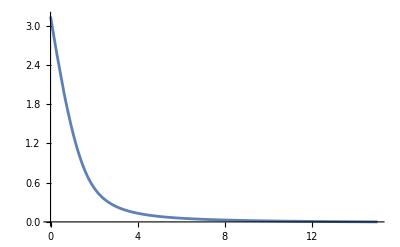

```mathematica
Plot[sf0[r],{r,η,R},PlotRange->{0,π}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
datasf0=Table[Flatten@{r,sf0[r]},{r,0.001,R,0.01}];
Export["data_sf0.txt",datasf0,"TSV"]
```

data_sf0.txt

### Massive

```mathematica
M = 0.528;η=0.001;R=15;tol=10^-4;
Final=False;αmin=0;αmax=10;
```

```mathematica
While[Final==False,α0=0.5 (αmin+αmax);sfm=NDSolve[{eomLm==0,f[η]==π-α0 η,f'[η]==-α0},f,{r,η,R}]//Last//Last//Last;Print[{α0,sfm[R]}];If[Abs[sfm[R]]<tol,Final=True,If[sfm[R]>0,αmin=α0,αmax=α0]]]
```

{5.,-3.06109}

{2.5,-3.30157}

{1.25,3.02524}

{1.875,3.26807}

{2.1875,4.23703}

{2.34375,-4.17192}

{2.26563,-0.70881}

{2.22656,4.17884}

{2.24609,3.42994}

{2.25586,2.09111}

{2.26074,0.835927}

{2.26318,0.0672174}

{2.2644,-0.325835}

{2.26379,-0.129691}

{2.26349,-0.0312289}

{2.26334,0.017997}

{2.26341,-0.00662193}

{2.26337,0.00568671}

{2.26339,-0.000466726}

{2.26338,0.00261028}

{2.26339,0.00108491}

{2.26339,0.000301615}

{2.26339,-0.0000686378}

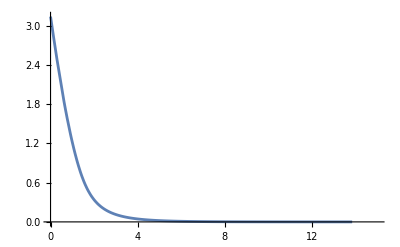

```mathematica
Plot[sfm[r],{r,η,R},PlotRange->{0,π}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
datasfm=Table[Flatten@{r,sfm[r]},{r,0.001,R,0.01}];
Export["data_sfm.txt",datasfm,"TSV"]
```

data_sfm.txt

### Sextic

```mathematica
M = 0.528; c6 = 1;η=0.001;R=15;tol=10^-4;
Final=False;αmin=0;αmax=10;
```

```mathematica
While[Final==False,α0=0.5 (αmin+αmax);sf6=NDSolve[{eomL6==0,f[η]==π-α0 η,f'[η]==-α0},f,{r,η,R}]//Last//Last//Last;Print[{α0,sf6[R]}];If[Abs[sf6[R]]<tol,Final=True,If[sf6[R]>0,αmin=α0,αmax=α0]]]
```

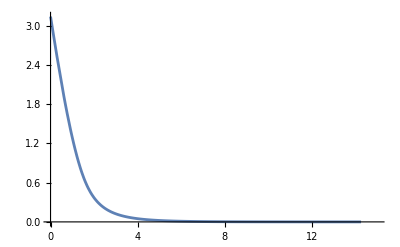

```mathematica
Plot[sf6[r],{r,η,R},PlotRange->{0,π}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
datasf6=Table[Flatten@{r,sf6[r]},{r,0.001,R,0.01}];
Export["data_sf6.txt",datasf6,"TSV"]
```

data_sf6.txt

### BPS

```mathematica
M = 0.528; c6 = 1;η=0.01;R=15;tol=10^-4;
Final=False;αmin=0;αmax=10;
```

```mathematica
While[Final==False,α0=0.5 (αmin+αmax);sfBPS=NDSolve[{eomLBPS==0,f[η]==π-α0 η,f'[η]==-α0},f,{r,η,R}]//Last//Last//Last;Print[{α0,sfBPS[R]}];If[Abs[sfBPS[R]]<tol,Final=True,If[sfBPS[R]>0,αmin=α0,αmax=α0]]]
```

```mathematica
Plot[sfBPS[r],{r,η,R},PlotRange->{0,π}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
datasfBPS=Table[Flatten@{r,sfBPS[r]},{r,0.001,R,0.01}];
Export["data_sfBPS.txt",datasfBPS,"TSV"]
```